# Morse key knob shape

This Mathematica code is used to construct the shape of the morse key knob, incorporated in the OpenSCAD source as a table.

## Dimpled disk knob

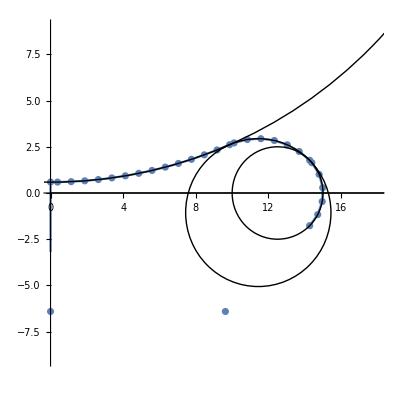

[[14.2678,4.64142], [14.7112,5.24278], [14.9572,5.94834], [14.9836,6.69506], [14.7882,7.41625], [14.3884,8.04748], [14.2678,8.17695], [13.691,8.65461], [13.0352,9.01637], [12.3236,9.24957], [11.5809,9.34602], [10.8333,9.30234], [10.1069,9.12007], [9.8615,9.02418], [9.16798,8.73871], [8.46621,8.47418], [7.75682,8.23082], [7.04045,8.00884], [6.31775,7.80845], [5.58936,7.62983], [4.85594,7.47314], [4.11815,7.33852], [3.37665,7.22609], [2.63212,7.13595], [1.88521,7.06819], [1.13661,7.02286], [0.386988,7.], [0,7.], [0,0.], [9.62635,0.], ]

```mathematica
(* Parameters for dimpled knob *)
C1={25/2,0}; (* Center of circle defining edge *)
r1=2.5; (* radius of edge, circle 1 *)
r2=4; (* radius of ridge, circle 2 *)
r3=25; (* radius of finger dimple, circle 3 *)
a1=45 Degree; (* slope at transition from edge to ridge *)

(* vector from center of circle 1 to ridge transition point *)
T1={Cos[a1],Sin[a1]}*r1;

(* center of ridge circle *)
C2=C1-T1*((r2-r1)/r1);

(* slope of line between centers of circles 2 and 3 *)
a2=ArcCos[C2[[1]]/(r2+r3)];

(* center of circle 3 *)
C3=C2+{-Cos[a2],Sin[a2]}*(r2+r3);

(* tabulate values from each of the circles, with given step length *)
stepmm=0.75; (* target step length along circles *)
hmincen=5+1.5+0.5; (* min thickness = min screw length + hole taper + margin *)
c1tbl=Table[C1+ {Cos[a],Sin[a]}*r1,{a,-45 Degree,a1,stepmm/r1}];
c2tbl=Table[C2+ {Cos[a],Sin[a]}*r2,{a,a1,3.14-a2,stepmm/r2}];
c3tbl=Table[C3+ {Cos[a],Sin[a]}*r3,{a,-a2,-3.14/2,-stepmm/r3}];

(* Add extra points for corners of profile *)
cenmin=c3tbl[[-1,2]];
edgestart=c1tbl[[1]];
edgestarty=edgestart[[2]];
extratbl={
{0,cenmin},
{0,cenmin-hmincen},
{edgestart[[1]]+(cenmin-hmincen)-edgestart[[2]],cenmin-hmincen}
};

(* join complete curve and shift to baseline zero *)
curve=Join[
c1tbl,
c2tbl,
c3tbl,
extratbl];
Print[Show[
ListPlot[curve,Joined->False,  AspectRatio->1],
ListPlot[curve,Joined->True,  AspectRatio->1],
Graphics[
{Circle[C1,r1],Circle[C2,r2],Circle[C3,r3],
Line[{{0,0},{30,0}}]}],PlotRange->{{0,18},{-9,9}}]];

(* Shift up so that lowest points are at y=0 *)
curve=#-{0,Min[curve[[All,2]]]}& /@ curve;

(* Format shape as OpenSCAD polygon *)
"["<>StringJoin @@ ("["<>ToString[#[[1]]]<>","<>ToString[#[[2]]]<>"], "& /@ curve)<>"]"
```

## Grip knob (unfinished)

```mathematica
(* Parameters for grip knob *)
C1={25/2,0}; (* Center of circle defining edge *)
r1=2.5; (* radius of edge, circle 1 *)
r2=4; (* radius of ridge, circle 2 *)
r3=25; (* radius of finger dimple, circle 3 *)
a1=45 Degree; (* slope at transition from edge to ridge *)

(* vector from center of circle 1 to ridge transition point *)
T1={Cos[a1],Sin[a1]}*r1;

(* center of ridge circle *)
C2=C1-T1*((r2-r1)/r1);

(* slope of line between centers of circles 2 and 3 *)
a2=ArcCos[C2[[1]]/(r2+r3)];

(* center of circle 3 *)
C3=C2+{-Cos[a2],Sin[a2]}*(r2+r3);

(* tabulate values from each of the circles, with given step length *)
stepmm=0.75; (* target step length along circles *)
hmincen=5+1.5+0.5; (* min thickness = min screw length + hole taper + margin *)
c1tbl=Table[C1+ {Cos[a],Sin[a]}*r1,{a,-45 Degree,a1,stepmm/r1}];
c2tbl=Table[C2+ {Cos[a],Sin[a]}*r2,{a,a1,3.14-a2,stepmm/r2}];
c3tbl=Table[C3+ {Cos[a],Sin[a]}*r3,{a,-a2,-3.14/2,-stepmm/r3}];

(* Add extra points for corners of profile *)
cenmin=c3tbl[[-1,2]];
edgestart=c1tbl[[1]];
edgestarty=edgestart[[2]];
extratbl={
{0,cenmin},
{0,cenmin-hmincen},
{edgestart[[1]]+(cenmin-hmincen)-edgestart[[2]],cenmin-hmincen}
};

(* join complete curve and shift to baseline zero *)
curve=Join[
c1tbl,
c2tbl,
c3tbl,
extratbl];
Print[Show[
ListPlot[curve,Joined->False,  AspectRatio->1],
ListPlot[curve,Joined->True,  AspectRatio->1],
Graphics[
{Circle[C1,r1],Circle[C2,r2],Circle[C3,r3],
Line[{{0,0},{30,0}}]}],PlotRange->{{0,18},{-9,9}}]];

(* Shift up so that lowest points are at y=0 *)
curve=#-{0,Min[curve[[All,2]]]}& /@ curve;

(* Format shape as OpenSCAD polygon *)
"["<>StringJoin @@ ("["<>ToString[#[[1]]]<>","<>ToString[#[[2]]]<>"], "& /@ curve)<>"]"
```

-Graphics-

[[14.2678,4.64142], [14.7112,5.24278], [14.9572,5.94834], [14.9836,6.69506], [14.7882,7.41625], [14.3884,8.04748], [14.2678,8.17695], [13.691,8.65461], [13.0352,9.01637], [12.3236,9.24957], [11.5809,9.34602], [10.8333,9.30234], [10.1069,9.12007], [9.8615,9.02418], [9.16798,8.73871], [8.46621,8.47418], [7.75682,8.23082], [7.04045,8.00884], [6.31775,7.80845], [5.58936,7.62983], [4.85594,7.47314], [4.11815,7.33852], [3.37665,7.22609], [2.63212,7.13595], [1.88521,7.06819], [1.13661,7.02286], [0.386988,7.], [0,7.], [0,0.], [9.62635,0.], ]